### custom

#### data

```mathematica
list=Tuples[Range[0,10,0.1],2];
low={{1,1},{1,2},{0,0},{1.5,3},{3,3},{3,1.5},{4,2.5},{4,3.5},{3,4},{1.5,1.5},{2,4},{1,4},{1,4.5},{1.25,2.6},{0.25,3}};
high={{3.5,2},{4,4},{4,2},{5,0},{3,1},{2,0.35},{3,0.5},{3.25,1.3},{4,1},{4.5,1.9},{4.5,3.75},{4.5,3}};
```

#### graph

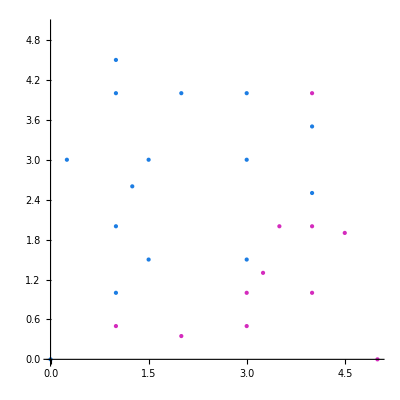

```mathematica
ListPlot[Tooltip@{low,high},PlotRange->{{0,5},{0,5}},PlotStyle->{{RGBColor[0.11,0.49,0.89],PointSize[Large]},{RGBColor[0.83,0.17,0.74],PointSize[Large]}},AspectRatio->Full]
```

#### Manipulate

```mathematica
Manipulate[ListPlot[Tooltip@{low,high,{{x,y}}},PlotRange->{{0,5},{0,5}},PlotStyle->{{RGBColor[0.11,0.49,0.89],PointSize[Large]},{RGBColor[0.83,0.17,0.74],PointSize[Large]},{SVM[{x,y}],PointSize[0.04]}},AspectRatio->Full],{x,0,5},{y,0,5}]
```

ListPlot::lpn: {{},{},{{3.04,1.65}}} is not a list of numbers or pairs of numbers.

#### Linear Kernel

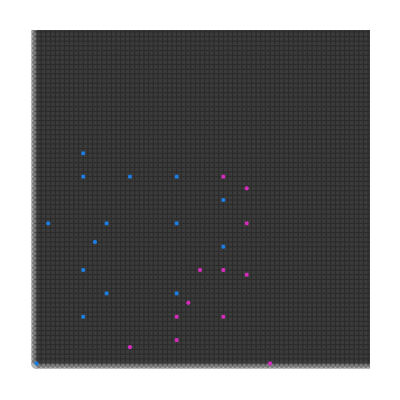

```mathematica
SVM=Classify[<|RGBColor[0.11,0.49,0.89]->low,RGBColor[0.83,0.17,0.74]->high|>,Method->{"SupportVectorMachine","KernelType"->"Linear","SoftMarginParameter"->100}];
colours=ParallelMap [SVM,list];
Show[Graphics[{Opacity[0.3],PointSize[0.02],Point[list,VertexColors->colours]},FrameLabel->{"x","y"},PlotRange->{{0,7},{0,7}},AspectRatio->Full,Options@ListPlot],ListPlot[Tooltip@{low,high},PlotRange->{{0,5},{0,5}},PlotStyle->{{RGBColor[0.11,0.49,0.89],PointSize[Large]},{RGBColor[0.83,0.17,0.74],PointSize[Large]}},AspectRatio->Full]]
```

#### Low Bias/High variance

```mathematica
SVM=Classify[<|RGBColor[0.11,0.49,0.89]->low,RGBColor[0.83,0.17,0.74]->high|>,Method->{"SupportVectorMachine","KernelType"->"Polynomial","BiasParameter"->0,"PolynomialDegree"->5}];
colours=ParallelMap [SVM,list];
Show[Graphics[{Opacity[0.3],PointSize[0.02],Point[list,VertexColors->colours]},FrameLabel->{"x","y"},PlotRange->{{0,7},{0,7}},AspectRatio->Full,Options@ListPlot],ListPlot[Tooltip@{low,high},PlotRange->{{0,5},{0,5}},PlotStyle->{{RGBColor[0.11,0.49,0.89],PointSize[Large]},{RGBColor[0.83,0.17,0.74],PointSize[Large]}},AspectRatio->Full]]
```

-Graphics-

#### Higher Bias

```mathematica
SVM=Classify[<|RGBColor[0.11,0.49,0.89]->low,RGBColor[0.83,0.17,0.74]->high|>,Method->{"SupportVectorMachine","KernelType"->"Polynomial","BiasParameter"->3,"PolynomialDegree"->5}];
colours=ParallelMap [SVM,list];
Show[Graphics[{Opacity[0.3],PointSize[0.02],Point[list,VertexColors->colours]},FrameLabel->{"x","y"},PlotRange->{{0,7},{0,7}},AspectRatio->Full,Options@ListPlot],ListPlot[Tooltip@{low,high},PlotRange->{{0,50},{0,50}},PlotStyle->{{RGBColor[0.11,0.49,0.89],PointSize[Large]},{RGBColor[0.83,0.17,0.74],PointSize[Large]}},AspectRatio->Full]]
```

-Graphics-

### flower

#### data

```mathematica
label[func_]:=Labeled[func,{"Sepal Width","Petal Length"},{Bottom,Left},RotateLabel->True]
flowerlist=Tuples[Range[0,8,0.1],2];
flowerlist2={#}&/@Tuples[Range[0,8,0.2],2];
Virginica={{3.2, 4.7}, {3.2, 4.5}, {3.1, 4.9}, {2.3, 4.}, {2.8, 4.6}, {2.8, 
     4.5}, {3.3, 4.7}, {2.4, 3.3}, {2.9, 4.6}, {2.7, 3.9}, {2., 3.5}, {3., 4.2}, {2.2, 4.}, {2.9, 4.7}, {2.9, 3.6}, {3.1, 4.4}, {3., 4.5}, {2.7, 4.1}, {2.2, 
     4.5}, {2.5, 3.9}, {3.2, 4.8}, {2.8, 4.}, {2.5, 4.9}, {2.8, 4.7}, {2.9, 4.3}, {3., 4.4}, {2.8, 4.8}, {3., 5.}, {2.9, 4.5}, {2.6, 3.5}, {2.4, 3.8}, {2.4, 
     3.7}, {2.7, 3.9}, {2.7, 5.1}, {3., 4.5}, {3.4, 4.5}, {3.1, 4.7}, {2.3, 4.4}, {3., 4.1}, {2.5, 4.}, {2.6, 4.4}, {3., 4.6}, {2.6, 4.}, {2.3, 3.3}, {2.7, 4.2}, 
     {3., 4.2}, {2.9, 4.2}, {2.9, 4.3}, {2.5, 3.}, {2.8, 4.1}};
VersiColor={{3.3, 6.}, {2.7, 5.1}, {3., 5.9}, {2.9, 5.6}, {3., 5.8}, {3., 6.6}, {2.5, 4.5}, {2.9, 6.3}, {2.5, 5.8}, {3.6, 6.1}, {3.2, 5.1}, {2.7, 5.3}, {3., 5.5}, 
     {2.5, 5.}, {2.8, 5.1}, {3.2, 5.3}, {3., 5.5}, {3.8, 6.7}, {2.6, 6.9}, {2.2, 5.}, {3.2, 5.7}, {2.8, 4.9}, {2.8, 6.7}, {2.7, 4.9}, {3.3, 5.7}, {3.2, 6.}, 
     {2.8, 4.8}, {3., 4.9}, {2.8, 5.6}, {3., 5.8}, {2.8, 6.1}, {3.8, 6.4}, {2.8, 5.6}, {2.8, 5.1}, {2.6, 5.6}, {3., 6.1}, {3.4, 5.6}, {3.1, 5.5}, {3., 4.8}, 
     {3.1, 5.4}, {3.1, 5.6}, {3.1, 5.1}, {2.7, 5.1}, {3.2, 5.9}, {3.3, 5.7}, {3., 5.2}, {2.5, 5.}, {3., 5.2}, {3.4, 5.4}, {3., 5.1}};
```

#### graph

```mathematica
-Graphics--Graphics-
```

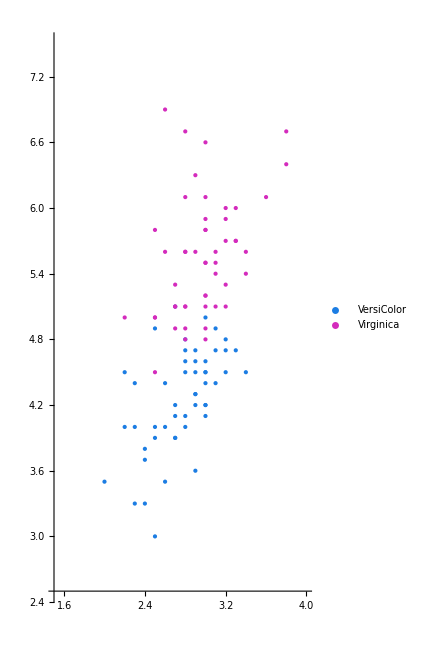
-Graphics-Sepal WidthPetal Length

```mathematica
label@ListPlot[{Virginica,VersiColor},PlotRange->{{1.5,4},{2.5,7.5}},PlotStyle->{{RGBColor[0.11,0.49,0.89],PointSize[Large]},{RGBColor[0.83,0.17,0.74],PointSize[Large]}},AspectRatio->Full,PlotLegends->{"VersiColor","Virginica"}]
```

#### High Gamma scaling Parameter ⟹ Overfit

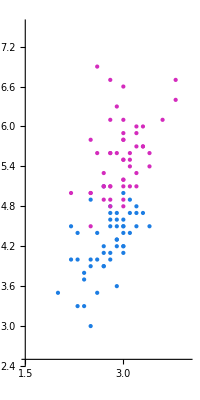
```mathematica
SVMFlower=Classify[<|RGBColor[0.11,0.49,0.89]->Virginica,RGBColor[0.83,0.17,0.74]->VersiColor|>,Method->{"SupportVectorMachine","KernelType"->"RadialBasisFunction","GammaScalingParameter"->35}];
colours=ParallelMap [SVMFlower,flowerlist];
Show[Legended[Graphics[{Opacity[0.3],PointSize[0.02],Point[flowerlist,VertexColors->colours]},FrameLabel->{"Sepal Width","Petal Length"},PlotRange->{{1.5,4},{2.5,7.5}},AspectRatio->Full,Options@ListPlot],Grid@{{RGBColor[0.83,0.17,0.74],"Virginica"},{RGBColor[0.11,0.49,0.89], "VersiColor"}}],-Graphics-]
```

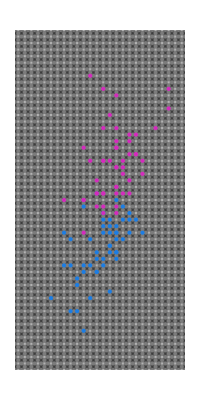

#### Linear: Ideal Model

```mathematica
SVMFlower=Classify[<|RGBColor[0.11,0.49,0.89]->Virginica,RGBColor[0.83,0.17,0.74]->VersiColor|>,Method->{"SupportVectorMachine","SoftMarginParameter"->50,"KernelType"->"Linear"}];
colours=ParallelMap [SVMFlower,flowerlist];
Show[Legended[Graphics[{Opacity[0.3],PointSize[0.02],Point[flowerlist,VertexColors->colours]},FrameLabel->{"Sepal Width","Petal Length"},PlotRange->{{1.5,4},{2.5,7.5}},AspectRatio->Full,Options@ListPlot],Grid@{{RGBColor[0.83,0.17,0.74],"Virginica"},{RGBColor[0.11,0.49,0.89], "VersiColor"}}],-Graphics-]
```

-Graphics-

#### Use

```mathematica
-Graphics--Graphics-
```

```mathematica
SVMFlower=Classify[<|RGBColor[0.11,0.49,0.89]->Virginica,RGBColor[0.83,0.17,0.74]->VersiColor|>,Method->{"SupportVectorMachine","SoftMarginParameter"->1}];
```

```mathematica
Manipulate[If[SVMFlower[{width,length}]===RGBColor[0.11, 0.49, 0.89],RGBColor[0.11, 0.49, 0.89]"Setosa",RGBColor[0.83, 0.17, 0.74]"Virginica"],{width,1,10},{length,1,10}]
```